# Generate Ill-conditioned distribution with rank-deficient cov

## Base ill-conditioned distribution

```mathematica
n=2;
e=0.01;
cov={{1, 1-e},{1-e,1}};
zero=0&/@Range@n;
normal=MultinormalDistribution[zero,cov];
pdf[x_,y_]=PDF[normal,{x,y}]
```

1.12822 ⅇ^(1/2 (-x (50.2513 x-49.7487 y)-y (-49.7487 x+50.2513 y)))

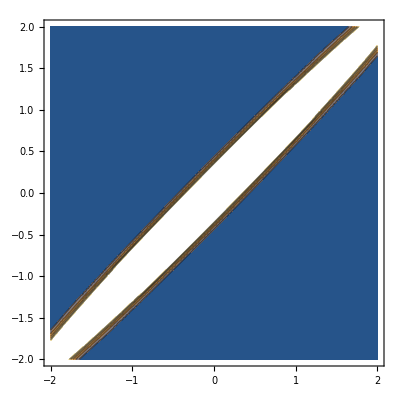

```mathematica
ContourPlot[pdf[x,y],{x,-2,2},{y,-2,2}]
```

## Add redundant component x2=x0+x1

```mathematica
(* Batch dimension is last one *)
dsize=1000;
SeedRandom[0];
X=RandomVariate[normal,{dsize}]//Transpose;
(* Augment with third component being sum of first two *)
Xa= X~Join~{{1,1}.X };

w={1,1, 0};
Y=Dot[w, Xa];
XY = Xa~Join~{Y};
Export["~/git/whitening/exp/linear-rankdeficient.csv",XY]
```

~/git/whitening/exp/linear-rankdeficient.csv

```mathematica
XY//Dimensions
```

{4,1000}

```mathematica
covE=X.Transpose[X]/dsize;
```

```mathematica
Eigenvalues[covE]
```

{6.21845,0.0103625,-6.41684×10^-16}

```mathematica
SingularValueDecomposition[covE][[2]]//Diagonal
```

{6.21845,0.0103625,0.}

## Try gradient descent with preconditioners

```mathematica
X//Transpose//First
```

{-0.619487,-0.710026}

```mathematica
Xa//Transpose//First
```

{-0.619487,-0.710026,-1.32951}

```mathematica
Inverse[X.Xᵀ]//MatrixForm
```

(0.0485219 | -0.0480095
-0.0480095 | 0.0484619)

```mathematica
PseudoInverse[X.Xᵀ]//MatrixForm
```

(0.0485219 | -0.0480095
-0.0480095 | 0.0484619)

```mathematica
Inverse[Xa.Xaᵀ]//MatrixForm
```

Inverse::luc: Result for Inverse of badly conditioned matrix {{1040.94,1031.23,2072.17},{1031.23,1042.23,2073.46},{2072.17,2073.46,4145.63}} may contain significant numerical errors.

(3.7002×10^12 | 3.7002×10^12 | -3.7002×10^12
3.7002×10^12 | 3.7002×10^12 | -3.7002×10^12
-3.7002×10^12 | -3.7002×10^12 | 3.7002×10^12)

```mathematica
PseudoInverse[Xa.Xaᵀ]//MatrixForm
```

(0.0482875 | -0.0482239 | 0.0000636205
-0.0482239 | 0.0482675 | 0.0000435894
0.0000636205 | 0.0000435894 | 0.00010721)

```mathematica
MatrixForm/@SingularValueDecomposition[X.Xᵀ]
```

{(-0.706885 | -0.707328
-0.707328 | 0.706885),(2072.82 | 0.
0. | 10.3625),(-0.706885 | -0.707328
-0.707328 | 0.706885)}

```mathematica
MatrixForm/@SingularValueDecomposition[Xa.Xaᵀ]
```

{(-0.408121 | 0.70718 | -0.57735
-0.408376 | -0.707033 | -0.57735
-0.816497 | 0.000147022 | 0.57735),(6218.45 | 0. | 0.
0. | 10.3625 | 0.
0. | 0. | 0.),(-0.408121 | 0.70718 | -0.57735
-0.408376 | -0.707033 | -0.57735
-0.816497 | 0.000147022 | 0.57735)}

```mathematica
loss[w_]:=Module[{error},
error=(w.X-Y);
Norm[error]^2/dsize
];
lossa[wa_]:=Module[{error},
error=(wa.Xa-Y);
Norm[error]^2/dsize
];
wa0={2,1,0} (* augmented w0 *)
grada[w_]:=2(w.Xa-Y).Transpose[Xa]/dsize; (* grad for augmented problem *)
optimize[pre_,lr_]:=Module[{},
gradstepa[w_]:=w-lr*pre.grada[w];
pointsa=NestList[gradstepa,wa0,100];
points=pointsa[[All,1;;2]];
plt1=ContourPlot[loss[{x,y}],{x,-2,2},{y,-2,2},Contours->100,ContourShading->None];
plt2=ListPlot[points,Joined->True,PlotStyle->PointSize[Medium],PlotRange->All];
plt3=Graphics[{Red,PointSize[0.005],Point@points}];
Show[plt1,plt2,plt3]
]
```

{2,1,0}

```mathematica
loss[w0]
```

1.04094

```mathematica
lossa[wa0]
```

1.04094

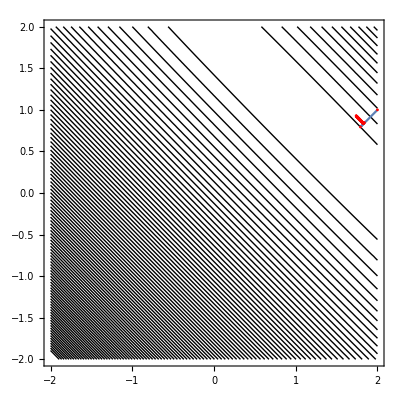

```mathematica
optimize[IdentityMatrix[3],0.1]
```

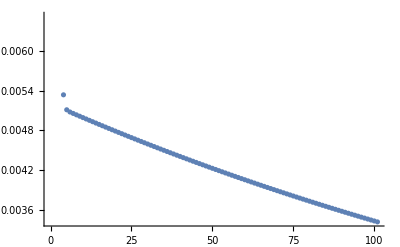

```mathematica
lossesa0 = lossa/@pointsa;
ListPlot[lossesa0]
```

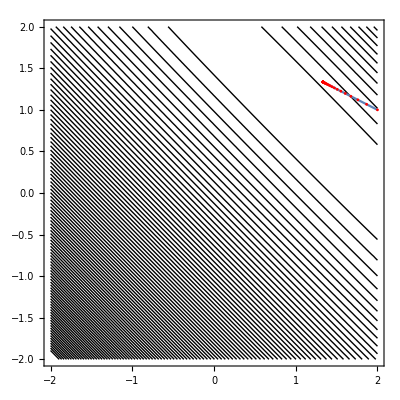

```mathematica
optimize[PseudoInverse[Xa.Xaᵀ/dsize],0.1]
```

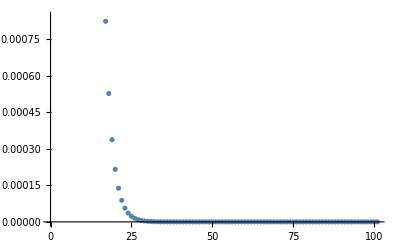

```mathematica
lossesa1= lossa/@pointsa;
ListPlot@lossesa1
```

## Express Pseudoinverse in terms of SVD

```mathematica
Eigenvalues[cova]
```

{6.21845,0.0103625,-6.41684×10^-16}

```mathematica
{U,S,W}=SingularValueDecomposition[cova]
```

{{{-0.408121,0.70718,0.57735},{-0.408376,-0.707033,0.57735},{-0.816497,0.000147022,-0.57735}},{{6.21845,0.,0.},{0.,0.0103625,0.},{0.,0.,0.}},{{-0.408121,0.70718,-0.57735},{-0.408376,-0.707033,-0.57735},{-0.816497,0.000147022,0.57735}}}

```mathematica
Si=Map[If[#<1*^-10,#,1/#]&,S,{2}];
```

```mathematica
Si
```

{{0.160812,0.,0.},{0.,96.5014,0.},{0.,0.,0.}}

```mathematica
U.Si.Transpose[W]
```

{{48.2875,-48.2239,0.0636205},{-48.2239,48.2675,0.0435894},{0.0636205,0.0435894,0.10721}}

```mathematica
PseudoInverse[cova]
```

{{48.2875,-48.2239,0.0636205},{-48.2239,48.2675,0.0435894},{0.0636205,0.0435894,0.10721}}

```mathematica
cova
```

{{1.04094,1.03123,2.07217},{1.03123,1.04223,2.07346},{2.07217,2.07346,4.14563}}